1/(γ^4 (1-√(1-1/γ^2) Cos[θ])^4)

(16 γ^4)/((1+γ^2 θ^2)^4)

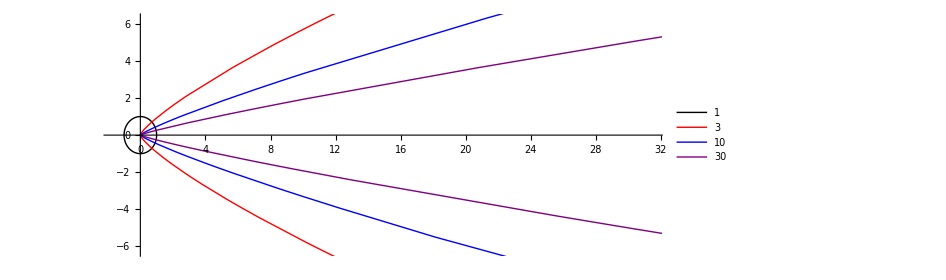

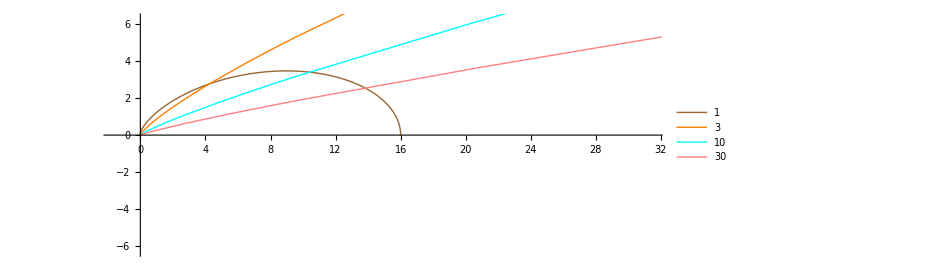

```mathematica
P[γ_,θ_]=1/γ^4*1/((1-Cos[θ] √(1-1/γ^2))^4)
Papprox[γ_,θ_]=((2 γ)/(1+γ^2 θ^2))^4
γo={1,3,10,30};

p1=PolarPlot[Evaluate[P[γo,θ]],{θ,0,2Pi},PlotLegends->γo,PlotStyle->{Black,Red,Blue,Purple},PlotRange->{{-π/2,10π},{-2π,2π}},ImageSize->700]
p2=PolarPlot[Evaluate[Papprox[γo,θ]],{θ,0,2Pi},PlotStyle->{Brown,Orange,Cyan,Pink},PlotRange->{{-π/2,10π},{-2π,2π}},ImageSize->700,PlotLegends->γo]
Show[p1,p2,ImageSize->700]
```

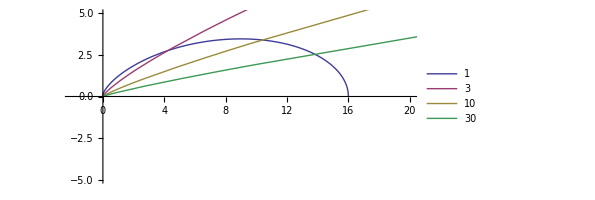

```mathematica
P[gamma_,theta_]:=(2*gamma/(1+gamma^2*theta^2))^4
gamma={1,3,10,30};
PolarPlot[Evaluate[P[gamma,theta]],{theta,0,2Pi},PlotLegends->gamma,PlotRange->{{-2,20},{-5,5}}]
```

```mathematica
P[gamma_,theta_]:=1/(gamma^4*(1-Sqrt[1-1/gamma^2]*Cos[theta])^4)
Papprox[gamma_,theta_]:=(2*gamma/(1+gamma^2*theta^2))^4
gamma={1,3,10,30};
p1=PolarPlot[P[gamma,theta],{theta,0,2Pi},PlotLegends->gamma,PlotRange->{{-2,20},{-5,5}}];
p2=PolarPlot[Papprox[gamma,theta],{theta,0,2Pi},PlotLegends->gamma,PlotRange->{{-2,20},{-5,5}},PlotStyle->{Dashed}];
```

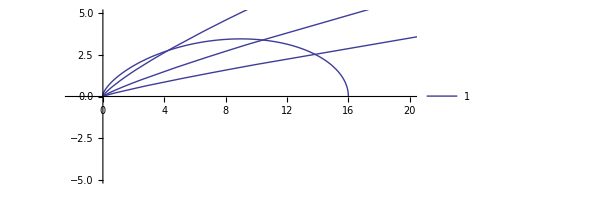

```mathematica
P[gamma_,theta_]:=(2*gamma/(1+gamma^2*theta^2))^4
gamma={1,3,10,30};
PolarPlot[P[gamma,theta],{theta,0,2Pi},PlotLegends->gamma,PlotRange->{{-2,20},{-5,5}}]
```